# Mendelian Model Solution

Hello and welcome to the solution to our final project. As always, please try to solve the project yourself before watching this video.

## Introduction

In this lecture, the second and last part of the final project, we will make use of our project template. If you didn’t use the project template, you might want to open it up and follow along.

## Constants

As we did in part 1, let’s evaluate our constants:

```mathematica
xmin=0;xmax=50;
ymin=0;ymax=50;
```

```mathematica
latinGenes={"A","B","C","D"};
numberGenes={"1","2","3","4"};
```

## Creatures

```mathematica
bc1=BlendingCreature[0.1,{20,40}];
bc2=BlendingCreature[0.4,{30,40}];
bc3=BlendingCreature[0.7,{40,30}];
bc4=BlendingCreature[0.9,{40,20}];
mc1=MendelianCreature[{"A","1"},{25,45}];
mc2=MendelianCreature[{"B","3"},{35,45}];
mc3=MendelianCreature[{"D","1"},{45,35}];
mc4=MendelianCreature[{"C","4"},{45,25}];
```

## Accessors

Since our BlendingCreatures and MendelianCreatures both have their Traits and Location in the same position, we can reuse the code by simply changing the pattern of Traits and Location to match either BlendingCreatures or MendelianCreatures:

```mathematica
Traits[creature:_BlendingCreature|_MendelianCreature]:=creature[[1]]
```

```mathematica
Location[creature:_BlendingCreature|_MendelianCreature]:=creature[[2]]
```

Let’s test that out now:

### Tests

#### Verify the accessors

```mathematica
Traits[bc1]===0.1
```

True

```mathematica
Traits[bc2]===0.4
```

True

```mathematica
Location[bc3]==={40,30}
```

True

```mathematica
Location[bc4]==={40,20}
```

True

```mathematica
Traits[mc1]==={"A","1"}
```

True

```mathematica
Traits[mc2]==={"B","3"}
```

True

```mathematica
Location[mc3]==={45,35}
```

True

```mathematica
Location[mc4]==={45,25}
```

True

Awesome.

## Evolution

In part 1, we wrote the Procreate function to evolve two BlendingCreatures by blending their traits. Here is the implementation:

```mathematica
Procreate[mother_BlendingCreature,father_BlendingCreature,OptionsPattern[{ChildCount->1}]]:=
Table[
BlendingCreature[
Mean[{Traits[father],Traits[mother]}],
{Random[Integer,{xmin,xmax}],Random[Integer,{ymin,ymax}]}
],
OptionValue[ChildCount]]
```

Now we need a Procreate function that will evolve two MendelianCreatures. In the Blending Model, we would take the average of the traits of the father and mother. In the Mendelian Model, we must pick between discrete genes from the father and mother.

We can actually reuse the implementation of Procreate we have for BlendingCreatures. We simply need to replace the line that produces the Mean of the Traits with another function that picks Traits at random from the father and mother. We can do that pretty easily with RandomChoice:

```mathematica
?RandomChoice
```

RowBox[{"RandomChoice", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] gives a pseudorandom choice of one of the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"RandomChoice", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives a list of StyleBox["n", "TI"] pseudorandom choices. 
RowBox[{"RandomChoice", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives an SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]]×SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]×… array of pseudorandom choices. 
RowBox[{"RandomChoice", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["w", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "→", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives a pseudorandom choice weighted by the SubscriptBox[StyleBox["w", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"RandomChoice", "[", RowBox[{RowBox[{StyleBox["wlist", "TI"], "→", StyleBox["elist", "TI"]}], ",", StyleBox["n", "TI"]}], "]"}] gives a list of StyleBox["n", "TI"] weighted choices.
RowBox[{"RandomChoice", "[", RowBox[{RowBox[{StyleBox["wlist", "TI"], "→", StyleBox["elist", "TI"]}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives an SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]]×SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]×… array of weighted choices.

Let’s use the first form, and pass the Traits of mc1 and mc2 as a test:

```mathematica
RandomChoice[{Traits[mc1],Traits[mc2]}]
```

{A,1}

Great. So now, we can reuse the implementation of Procreate for BlendingCreatures:

```mathematica
Procreate[father_MendelianCreature,mother_MendelianCreature,OptionsPattern[{ChildCount->1}]]:=
Table[
MendelianCreature[
(* And we replace this line with our RandomChoice using father for mc1 and mother for mc2 *)
RandomChoice[{Traits[father],Traits[mother]}],
{Random[Integer,{xmin,xmax}],Random[Integer,{ymin,ymax}]}
],OptionValue[ChildCount]]
```

Let’s test that out:

### Tests

#### Verify that Procreate of bc1 and bc2 produces offspring with trait value 0.25

```mathematica
MatchQ[Procreate[bc1,bc2],{BlendingCreature[0.25,{x_,y_}]}/;xmin≤x≤xmax&&ymin≤y≤ymax]
```

True

#### Verify that Procreate of bc1 and bc2 with ChildCount → 2 produces two BlendingCreature offspring

```mathematica
MatchQ[Procreate[bc1,bc2,ChildCount->2],offspring:{BlendingCreature[0.25,_]..}/;Length[offspring]==2]
```

True

#### Verify that Procreate of mc1 and mc3 produces offspring with trait value in {{A, 1}, {D, 1}}

```mathematica
MatchQ[Procreate[mc1,mc3],{MendelianCreature[{"A"|"D","1"},{x_,y_}]}/;xmin≤x≤xmax&&ymin≤y≤ymax]
```

True

#### Verify that Procreate of mc1 and mc2 produces offspring with trait value in {{A, 1}, {A, 3}, {B, 1}, {B, 3}}

```mathematica
MatchQ[Procreate[mc1,mc2],{MendelianCreature[{"A"|"B","1"|"3"},{x_,y_}]}/;xmin≤x≤xmax&&ymin≤y≤ymax]
```

True

#### Verify that Procreate of mc1 and mc2 with ChildCount → 2 produces two MendelianCreature offspring

```mathematica
MatchQ[Procreate[mc1,mc2,ChildCount->2],offspring:{MendelianCreature[_,_]..}/;Length[offspring]==2]
```

True

Awesome!

## Initialization

Here’s our function from part 1 that initialized a population of BlendingCreatures:

```mathematica
InitializeBlendingPopulation[size_Integer]:=Table[
BlendingCreature[
N@RandomChoice[{0,1}],
{Random[Integer,{xmin,xmax}],Random[Integer,{ymin,ymax}]}
],size]
```

We can modify InitializeBlendingPopulation to initialize our Mendelian population:

```mathematica
InitializeMendelianPopulation[size_Integer]:=Table[
MendelianCreature[
(* We just need to modify the RandomChoice to choose between the discrete genes *)
{RandomChoice[latinGenes],RandomChoice[numberGenes]},
{Random[Integer,{xmin,xmax}],Random[Integer,{ymin,ymax}]}
],size]
```

Let’s test it out:

### Tests

#### Verify that InitializeBlendingPopulation returns 20 BlendingCreatures

```mathematica
MatchQ[InitializeBlendingPopulation[20],creatures:{_BlendingCreature..}/;Length[creatures]==20]
```

True

#### Verify that InitializeMendelianPopulation returns 20 MendelianCreatures

```mathematica
MatchQ[InitializeMendelianPopulation[20],creatures:{MendelianCreature[{Alternatives@@latinGenes,Alternatives@@numberGenes},_]..}/;Length[creatures]==20]
```

True

Awesome!

## Simulation

The Evolve function from part 1 is completely agnostic to the kind of creature it works on. We’ve written Procreate to be able to handle both BlendingCreatures and MendelianCreatures. Therefore, our Evolve function can simply be modified so that it will match MendelianCreatures as well:

```mathematica
Evolve[population:{__BlendingCreature|__MendelianCreature}]:=Flatten[Procreate[Sequence@@#,ChildCount->2]&/@Partition[RandomSample[population],2]]
```

Here is our BlendingSimulate function from part 1:

```mathematica
BlendingSimulate[seed_Integer,numberOfGenerations_Integer,initialPopulationSize_Integer]:=
BlockRandom[
SeedRandom[seed];
BlendingSimulate[seed,numberOfGenerations,initialPopulationSize]=NestList[Evolve,InitializeBlendingPopulation[initialPopulationSize],numberOfGenerations-1]
]
```

We can reuse all of the code:

```mathematica
MendelianSimulate[seed_Integer,numberOfGenerations_Integer,initialPopulationSize_Integer]:=
BlockRandom[
SeedRandom[seed];
(* We're just going to change BlendingSimulate to MendelianSimulate *)
MendelianSimulate[seed,numberOfGenerations,initialPopulationSize]=
(* And InitializeBlendingPopulation to InitializeMendelianPopulation *)NestList[Evolve,InitializeMendelianPopulation[initialPopulationSize],numberOfGenerations-1]
]
```

Looks like all the hard work was in part 1! Here, we get to reuse the caching mechanism we implemented in part 1 as well. Finally, we need to implement the main Simulate function. We can do this with a call to Switch:

```mathematica
Simulate[seed_Integer,numberOfGenerations_Integer,initialPopulationSize_Integer,method_String]:=Switch[method,
"Blending",BlendingSimulate[seed,numberOfGenerations,initialPopulationSize],
"Mendelian",MendelianSimulate[seed,numberOfGenerations,initialPopulationSize]
]
```

### Tests

#### Verify that Evolving a Blending population produces a new population of the same size

```mathematica
With[{initPop=InitializeBlendingPopulation[20]},
With[{nextGen=Evolve[initPop]},
And[
MatchQ[nextGen,creatures:{_BlendingCreature..}/;Length[creatures]==20],
nextGen=!=initPop
]
]]
```

True

#### Verify that Evolving a Mendelian population produces a new population of the same size

```mathematica
With[{initPop=InitializeMendelianPopulation[20]},
With[{nextGen=Evolve[initPop]},
And[
MatchQ[nextGen,creatures:{_MendelianCreature..}/;Length[creatures]==20],
nextGen=!=initPop
]
]]
```

True

#### Verify that the Blending simulation is repeatable for the same arguments

```mathematica
BlendingSimulate[0,20,200]===BlendingSimulate[0,20,200]
```

True

#### Verify that the Mendelian simulation is repeatable for the same arguments

```mathematica
MendelianSimulate[0,20,200]===MendelianSimulate[0,20,200]
```

True

#### Verify that the Blending simulation produces different results for different seeds

```mathematica
BlendingSimulate[0,20,200]=!=BlendingSimulate[1,20,200]
```

True

#### Verify that the Mendelian simulation produces different results for different seeds

```mathematica
MendelianSimulate[0,20,200]=!=MendelianSimulate[1,20,200]
```

True

#### Verify that calling Simulate with the Blending parameter produces a BlendingCreature

```mathematica
MatchQ[Simulate[0,1,1,"Blending"],{{BlendingCreature_}}]
```

True

#### Verify that calling Simulate with the Mendelian parameter produces a MendelianCreature

```mathematica
MatchQ[Simulate[0,1,1,"Mendelian"],{{MendelianCreature_}}]
```

True

Awesome!

## Rendering

Next, let’s evaluate the provided ColorBinarize function:

```mathematica
ColorBinarize[color_RGBColor]:=Round[Mean[List@@color]]/.{0->White,1->Black}
```

Let’s also evaluate our HeredityColor for BlendingCreatures:

```mathematica
HeredityColor[creature_BlendingCreature]:=With[{
traits=Traits[creature]
},RGBColor[traits,traits,traits]]
```

For MendelianCreatures, we built our HeredityColor as follows:

```mathematica
HeredityColor[MendelianCreature[{latinGene_,numberGene_},_]]:=RGBColor[
Position[latinGenes,latinGene][[1,1]]/Length[latinGenes],
Position[numberGenes,numberGene][[1,1]]/Length[numberGenes],
0]
```

Evaluate CreatureName for BlendingCreatures:

```mathematica
CreatureName[creature_BlendingCreature]:=Round[Traits[creature],.1]
```

And the CreatureName for MendelianCreatures is simply StringJoin of the Traits:

```mathematica
CreatureName[creature_MendelianCreature]:=StringJoin[Traits[creature]]
```

Now we have the Render functions. It’s simple to modify them to work with MendelianCreatures as well:

```mathematica
Render[creature:_BlendingCreature|_MendelianCreature]:=With[{
color=HeredityColor[creature],
location=Location[creature]
},{
EdgeForm[Black],color,Disk[location,1],
ColorBinarize[color],Text[CreatureName[creature],location]
}]
```

```mathematica
Render[population:{___BlendingCreature|___MendelianCreature}]:=Render/@population
```

Evaluate our TraitHistogram function for BlendingCreatures:

```mathematica
TraitHistogram[population:{___BlendingCreature}]:=Histogram[Traits/@population,{0,1.1,.1},ChartStyle->Table[RGBColor[i,i,i],{i,0,1,0.1}]]
```

Now we need to build a histogram for MendelianCreatures. Let’s start by making a population that we can use to prototype:

```mathematica
population=InitializeMendelianPopulation[20]
```

{MendelianCreature[{D,2},{47,50}],MendelianCreature[{D,3},{48,38}],MendelianCreature[{C,1},{45,18}],MendelianCreature[{B,4},{34,47}],MendelianCreature[{D,2},{8,40}],MendelianCreature[{D,2},{25,33}],MendelianCreature[{A,3},{14,41}],MendelianCreature[{D,3},{8,11}],MendelianCreature[{D,1},{14,48}],MendelianCreature[{C,4},{32,30}],MendelianCreature[{A,1},{5,16}],MendelianCreature[{B,4},{35,48}],MendelianCreature[{C,3},{12,44}],MendelianCreature[{B,1},{2,7}],MendelianCreature[{A,3},{29,34}],MendelianCreature[{A,2},{17,49}],MendelianCreature[{A,3},{22,35}],MendelianCreature[{A,3},{14,34}],MendelianCreature[{B,4},{19,42}],MendelianCreature[{C,1},{43,10}]}

We want to extract all the individual genes and get a Tally of them. So let’s map Traits over the population:

```mathematica
Traits/@population
```

{{D,2},{D,3},{C,1},{B,4},{D,2},{D,2},{A,3},{D,3},{D,1},{C,4},{A,1},{B,4},{C,3},{B,1},{A,3},{A,2},{A,3},{A,3},{B,4},{C,1}}

Good. Now, in order to get an individual Tally of the genes, we need the letters and numbers to be in a flattened list:

```mathematica
Flatten[Traits/@population]
```

{D,2,D,3,C,1,B,4,D,2,D,2,A,3,D,3,D,1,C,4,A,1,B,4,C,3,B,1,A,3,A,2,A,3,A,3,B,4,C,1}

Now we can apply Tally:

```mathematica
Tally@Flatten[Traits/@population]
```

{{D,6},{2,4},{3,7},{C,4},{1,5},{B,4},{4,4},{A,6}}

Awesome. Let’s sort this so that it appears in a deterministic order:

```mathematica
Sort@Tally@Flatten[Traits/@population]
```

{{1,5},{2,4},{3,7},{4,4},{A,6},{B,4},{C,4},{D,6}}

We’ll now use a BarChart to render this. The first argument to BarChart are the tallies. We then pass the label for the bars in an option called CharLabels. So let’s hold our Tally in a With:

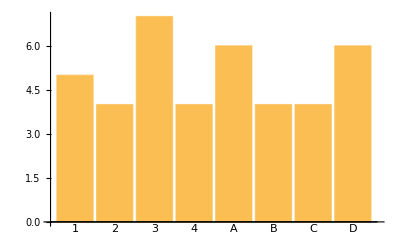

```mathematica
With[{tally=Sort@Tally@Flatten[Traits/@population]},
BarChart[tally[[;;,2]],ChartLabels->tally[[;;,1]]]]
```

Awesome. Now let’s get that extra credit. We need to apply the appropriate color to each bar. Here, {A, B, C, D} contribute to the red RGB component and {1, 2, 3, 4} contribute to the green RGB component. Let’s write a helper function that will produce the correct color for a given gene:

```mathematica
GeneColor[gene_/;MemberQ[latinGenes,gene]]:=
RGBColor[FirstPosition[latinGenes,gene][[1]]/Length[latinGenes],0,0]
```

```mathematica
GeneColor[gene_/;MemberQ[numberGenes,gene]]:=
RGBColor[0,FirstPosition[numberGenes,gene][[1]]/Length[numberGenes],0]
```

Now, we can generate the colors for ChartStyle by mapping GeneColor over the ChartLabels:

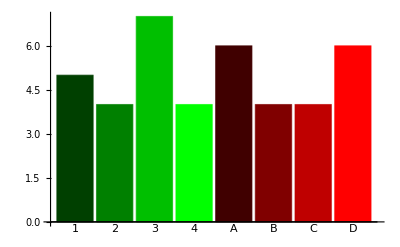

```mathematica
With[{tally=Sort@Tally@Flatten[Traits/@population]},
BarChart[tally[[;;,2]],ChartLabels->tally[[;;,1]],ChartStyle->GeneColor/@tally[[;;,1]]]]
```

That’s our function! Let’s add the function definition:

```mathematica
TraitHistogram[population:{___MendelianCreature}]:=
With[{tally=Sort@Tally@Flatten[Traits/@population]},
BarChart[tally[[;;,2]],ChartLabels->tally[[;;,1]],ChartStyle->GeneColor/@tally[[;;,1]]]]
```

Great! Let’s run our tests!

### Tests

#### Verify that HeredityColor of bc1 is GrayLevel of 0.1

```mathematica
ColorConvert[HeredityColor[bc1],"RGB"]===RGBColor[0.1,0.1,0.1]
```

True

#### Verify that HeredityColor of bc2 is GrayLevel of 0.4

```mathematica
ColorConvert[HeredityColor[bc2],"RGB"]===RGBColor[0.4,0.4,0.4]
```

True

#### Verify that HeredityColor of mc1

```mathematica
ColorConvert[HeredityColor[mc1],"RGB"]===RGBColor[0.25,0.25,0.]
```

True

#### Verify that HeredityColor of mc2

```mathematica
ColorConvert[HeredityColor[mc2],"RGB"]===RGBColor[.5,.75,0.]
```

True

#### Verify that rendering a Blending creature returns a list

```mathematica
MatchQ[Render[bc1],_List]
```

True

#### Verify that rendering a Mendelian creature returns a list

```mathematica
MatchQ[Render[mc1],_List]
```

True

#### Verify that rendering a Blending population returns a list

```mathematica
MatchQ[Render[InitializeBlendingPopulation[20]],_List]
```

True

#### Verify that rendering a Mendelian population returns a list

```mathematica
MatchQ[Render[InitializeMendelianPopulation[20]],_List]
```

True

#### Verify that we can render a column of graphics for a Blending simulation

This is not an automated test. Eyeball your render and make sure it looks like our render:

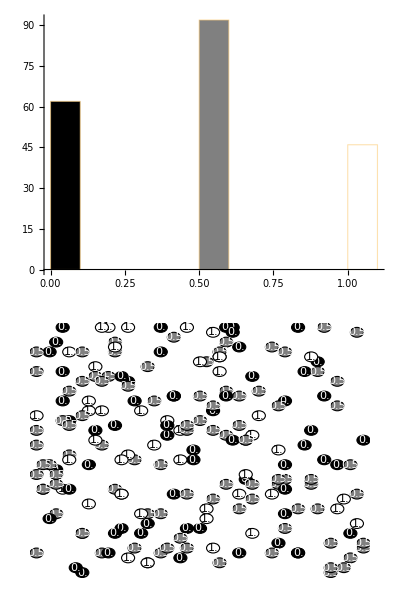

```mathematica
Column[{
TraitHistogram[BlendingSimulate[0,20,200][[2]]],
Graphics[Render[BlendingSimulate[0,20,200][[2]]],ImageSize->Large,PlotRange->{{xmin,xmax},{ymin,ymax}},ImagePadding->20]
}, Center]
```

Which should look something like:

-Graphics-

#### Verify that we can render a column of graphics for a Mendelian simulation

This is not an automated test. Eyeball your render and make sure it looks like our render:

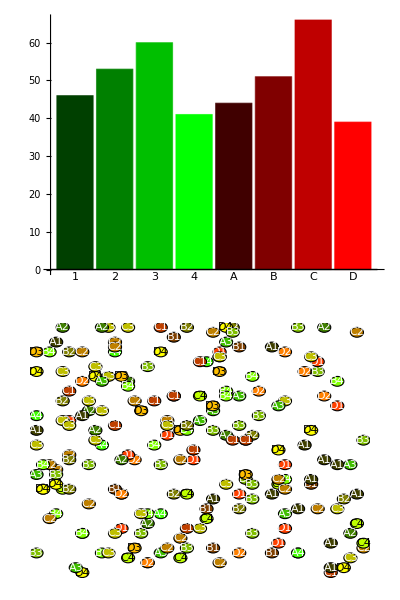

```mathematica
Column[{
TraitHistogram[MendelianSimulate[0,20,200][[2]]],
Graphics[Render[MendelianSimulate[0,20,200][[2]]],ImageSize->Large,PlotRange->{{xmin,xmax},{ymin,ymax}},ImagePadding->20]
}, Center]
```

Which should look something like:

-Graphics-

Awesome!

## Manipulate

We’re nearly there. We just need to update our Manipulate to support both Blending and Mendelian modes.

```mathematica
Manipulate[
Column[{
(* Next we change these lines to call our over-all Simulate function, passing method as an argument *)
TraitHistogram[Simulate[s,20,200,method][[t]]],
Graphics[Render[Simulate[s,20,200,method][[t]]],ImageSize->Large]
},Center],
{{s,0,"Seed"},0,100,1,Appearance->"Open"},
{{t,1,"Generation"},1,20,1,Appearance->"Open",AnimationRate->1},
(* First we add the Simulation Method button *)
{{method,"Blending","Simulation Method"},{"Blending","Mendelian"}}
]
```

There we have it! We can now simulate the Blending model, and watch how each generation converges to a single Trait value of 0.5. And we can also simulate the Mendelian model. You’ll notice that the number of genes might vary a lot over time, but it never converges to a single value. This is much closer to reality.

Congratulations on completing our course! I personally think that it was a difficult course. So, if you made it here, you should feel really proud of yourself. We really hope you had fun learning Mathematica with us, and we wish you good luck in your math and programming explorations! Thanks and, hopefully, see you at the next lecture!